```mathematica
(*Import packages*)
(*<< PVReduce`*)
(*Remove[PVReduce`Dot];*)
$LoadFeynArts = True;
$FeynCalcStartupMessages = False;
<< FeynCalc`
$FAVerbose = 0;
AppendTo[$Path, "C:\\Users\\Bruker\\Documents\\Skole\\master\\masteroppgave\\code\\mathematica\\include"];
<< XSec`
<< TreeLevel`
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

```mathematica
(*Why is this?*)
$KeepLogDivergentScalelessIntegrals=True;
```

## Get Feynman diagrams

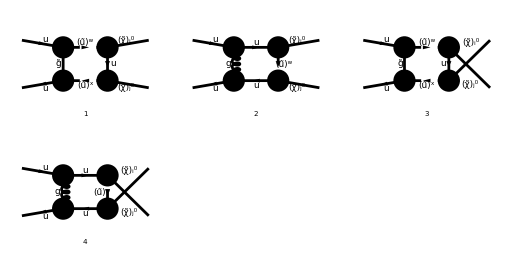

```mathematica
BoxDiagrams = InsertFields[CreateTopologies[1, 2->2,ExcludeTopologies->{Triangles,SelfEnergies,Tadpoles}], {F[3, {1,a}], -F[3, {1,b}]} -> {F[11, {i}], F[11, {j}]}, InsertionLevel -> {Classes}, Model -> MSSMQCD,Restrictions->{NoLightFHCoupling,NoElectronHCoupling},ExcludeParticles->{V[1],V[2],V[3],F[11],F[12],S[1],S[2],S[3],S[4]}];
Paint[BoxDiagrams, Numbering->Simple, ImageSize->{512,256}];
```

## Convert diagrams to amplitudes

```mathematica
(*Box-loop diagrams*)
Subscript[M, box][0]=FCFAConvert[CreateFeynAmp[BoxDiagrams], IncomingMomenta->{p1,p2}, OutgoingMomenta->{pi,pj},LoopMomenta->{qloop},ChangeDimension->D,UndoChiralSplittings->True,List->True,SMP->True,DropSumOver->True,LorentzIndexNames->{μ,ν}]//.AmpSimplifyRules;
```

```mathematica
(*Replacing couplings*)
Subscript[M, box][1]=Subscript[M, box][0]//.{SqrtEGl Conjugate[SqrtEGl]->1}//.QSimplifyRules//Simplify;
```

```mathematica
Subscript[M, box][2]=TraceLoopAmp[Subscript[M, box][1]];
```

```mathematica
Subscript[M, box][3]=EvalPVLoopAmp/@Subscript[M, box][2];
CheckPVRemainder/@Subscript[M, box][3]
```

{True,True,True,True}

```mathematica
Subscript[M, box][4]=Select[(SelectNotFree2[#1,{A0,B0,C0,D0}]&)/@Select[Subscript[M, box][3],CheckPVRemainder],(!PossibleZeroQ[#1-1]&)]
```

{1/(4 π^2)m_(g̃) D_0(0,s,m_i^2,t,0,m_j^2,m_(g̃)^2,m_((q̃)_Sfe6)^2,m_((q̃)_Sfe5)^2,0) (Conjugate[(C_iSfe5^L)] C_jSfe6^L (φ(p_j,m_j)).(γ·p_2).(γ̄)^6.(φ(-p_i,m_i))+Conjugate[(C_jSfe6^R)] C_iSfe5^R (φ(p_j,m_j)).(γ·p_2).(γ̄)^7.(φ(-p_i,m_i))-Conjugate[(C_iSfe5^L)] C_jSfe6^L (φ(p_j,m_j)).(γ̄)^6.(φ(-p_i,m_i)) m_j-Conjugate[(C_jSfe6^R)] C_iSfe5^R (φ(p_j,m_j)).(γ̄)^7.(φ(-p_i,m_i)) m_j) g_s^2 g_W^2 T_bCol5^Glu5 T_Col5a^Glu5 (Conjugate[((Q̃)_(Sfe6,1))] (φ(-p_2)).(γ̄)^6.(φ(p_1)) (Q̃)_(Sfe5,2) SqrtEGl^2+(Conjugate[SqrtEGl])^2 Conjugate[((Q̃)_(Sfe6,2))] (φ(-p_2)).(γ̄)^7.(φ(p_1)) (Q̃)_(Sfe5,1)),(D_0(0,s,m_i^2,t,0,m_j^2,0,0,0,m_((q̃)_Sfe5)^2) (Conjugate[(C_jSfe5^L)] (φ(-p_2)).(γ̄)^6.(φ(-p_j,m_j))+C_jSfe5^R (φ(-p_2)).(γ̄)^7.(φ(-p_j,m_j))) (Conjugate[(C_iSfe5^R)] (φ(p_i,m_i)).(γ·p_j).(γ·p_2).(γ̄)^6.(φ(p_1))+C_iSfe5^L (φ(p_i,m_i)).(γ·p_j).(γ·p_2).(γ̄)^7.(φ(p_1))+Conjugate[(C_iSfe5^R)] (φ(p_i,m_i)).(γ·p_2).(γ̄)^6.(φ(p_1)) m_i+C_iSfe5^L (φ(p_i,m_i)).(γ·p_2).(γ̄)^7.(φ(p_1)) m_i) g_s^2 g_W^2 T_bCol5^Glu5 T_Col5a^Glu5)/(4 π^2),-1/(4 π^2)m_(g̃) D_0(0,s,m_j^2,u,0,m_i^2,m_(g̃)^2,m_((q̃)_Sfe6)^2,m_((q̃)_Sfe5)^2,0) (Conjugate[(C_iSfe6^R)] C_jSfe5^R (φ(p_j,m_j)).(γ·p_2).(γ̄)^6.(φ(-p_i,m_i))+Conjugate[(C_jSfe5^L)] C_iSfe6^L (φ(p_j,m_j)).(γ·p_2).(γ̄)^7.(φ(-p_i,m_i))+Conjugate[(C_jSfe5^L)] C_iSfe6^L (φ(p_j,m_j)).(γ̄)^6.(φ(-p_i,m_i)) m_i+Conjugate[(C_iSfe6^R)] C_jSfe5^R (φ(p_j,m_j)).(γ̄)^7.(φ(-p_i,m_i)) m_i) g_s^2 g_W^2 T_bCol5^Glu5 T_Col5a^Glu5 (Conjugate[((Q̃)_(Sfe6,1))] (φ(-p_2)).(γ̄)^6.(φ(p_1)) (Q̃)_(Sfe5,2) SqrtEGl^2+(Conjugate[SqrtEGl])^2 Conjugate[((Q̃)_(Sfe6,2))] (φ(-p_2)).(γ̄)^7.(φ(p_1)) (Q̃)_(Sfe5,1)),-(D_0(0,s,m_j^2,u,0,m_i^2,0,0,0,m_((q̃)_Sfe5)^2) (Conjugate[(C_iSfe5^L)] (φ(-p_2)).(γ̄)^6.(φ(-p_i,m_i))+C_iSfe5^R (φ(-p_2)).(γ̄)^7.(φ(-p_i,m_i))) (Conjugate[(C_jSfe5^R)] (φ(p_j,m_j)).(γ·p_i).(γ·p_2).(γ̄)^6.(φ(p_1))+C_jSfe5^L (φ(p_j,m_j)).(γ·p_i).(γ·p_2).(γ̄)^7.(φ(p_1))+Conjugate[(C_jSfe5^R)] (φ(p_j,m_j)).(γ·p_2).(γ̄)^6.(φ(p_1)) m_j+C_jSfe5^L (φ(p_j,m_j)).(γ·p_2).(γ̄)^7.(φ(p_1)) m_j) g_s^2 g_W^2 T_bCol5^Glu5 T_Col5a^Glu5)/(4 π^2)}

```mathematica
Subscript[I, sbox][0]=SquareAmplitudes[Subscript[M, box][4],Subscript[M̄, s][0]]//.{SqrtEGl Conjugate[SqrtEGl]->1}//Simplify
Subscript[I, tbox][0]=SquareAmplitudes[Subscript[M, box][4],ReplaceAll[Subscript[M̄, t][0],A->B]]//.{SqrtEGl Conjugate[SqrtEGl]->1}//Simplify
Subscript[I, ubox][0]=SquareAmplitudes[Subscript[M, box][4],ReplaceAll[Subscript[M̄, u][0],A->B]]//.{SqrtEGl Conjugate[SqrtEGl]->1}//Simplify
```

{0,-(C_F g_s^2 g_W^4 δ_ab δ_ab D_0(0,s,m_i^2,t,0,m_j^2,0,0,0,m_((q̃)_Sfe5)^2) (C_iSfe5^L Conjugate[(C_jSfe5^L)] (Conjugate[(Z_s^L)] ((m_j^2-t) tr((γ·p_j).(γ·p_2).(γ·p_1).(γ·p_i).(γ̄)^5)+s t (D s-2 m_j^2+2 t+4 u)-2 s m_i^2 (m_j^2+t))+(D-2) s^2 m_i m_j Z_s^L)-C_jSfe5^R Conjugate[(C_iSfe5^R)] (Z_s^R ((t-m_j^2) tr((γ·p_j).(γ·p_2).(γ·p_1).(γ·p_i).(γ̄)^5)+s t (D s-2 m_j^2+2 t+4 u)-2 s m_i^2 (m_j^2+t))+(D-2) s^2 m_i m_j Conjugate[(Z_s^R)])))/(4 π^2 (cos(θ_W))^2 ((p_i+p_j)^2-m_Z^2)),0,(C_F g_s^2 g_W^4 δ_ab δ_ab D_0(0,s,m_j^2,u,0,m_i^2,0,0,0,m_((q̃)_Sfe5)^2) (C_iSfe5^R Conjugate[(C_jSfe5^R)] (Conjugate[(Z_s^R)] ((u-m_i^2) tr((γ·p_1).(γ·p_j).(γ·p_i).(γ·p_2).(γ̄)^5)+s u (D s-2 m_j^2+4 t+2 u)-2 s m_i^2 (m_j^2+u))+(D-2) s^2 m_i m_j Z_s^R)-C_jSfe5^L Conjugate[(C_iSfe5^L)] (Z_s^L ((m_i^2-u) tr((γ·p_1).(γ·p_j).(γ·p_i).(γ·p_2).(γ̄)^5)+s u (D s-2 m_j^2+4 t+2 u)-2 s m_i^2 (m_j^2+u))+(D-2) s^2 m_i m_j Conjugate[(Z_s^L)])))/(4 π^2 (cos(θ_W))^2 ((p_i+p_j)^2-m_Z^2))}

{(C_F m_(g̃) D_0(0,s,m_i^2,t,0,m_j^2,m_(g̃)^2,m_((q̃)_Sfe6)^2,m_((q̃)_Sfe5)^2,0) δ_ab g_s^2 g_W^4 δ_ab (Conjugate[((Q̃)_(Sfe6,1))] (2 s t Conjugate[(C_jSfe6^R)] C_iSfe5^R m_i+Conjugate[(C_iSfe5^L)] C_jSfe6^L (2 s t-tr((γ·p_i).(γ·p_1).(γ·p_2).(γ·p_j).(γ̄)^5)) m_j) Q_B^RL (Q̃)_(Sfe5,2) SqrtEGl^2+(Conjugate[SqrtEGl])^2 Conjugate[(Q_B^LR)] Conjugate[((Q̃)_(Sfe6,2))] (2 s t Conjugate[(C_iSfe5^L)] C_jSfe6^L m_i+Conjugate[(C_jSfe6^R)] C_iSfe5^R (2 s t+tr((γ·p_i).(γ·p_1).(γ·p_2).(γ·p_j).(γ̄)^5)) m_j) (Q̃)_(Sfe5,1)))/(4 π^2 ((p_2-p_j)^2-m_((q̃)_B)^2)),-1/(4 π^2 ((p_2-p_j)^2-m_((q̃)_B)^2))C_F D_0(0,s,m_i^2,t,0,m_j^2,0,0,0,m_((q̃)_Sfe5)^2) δ_ab (t-m_j^2) (Conjugate[(C_jSfe5^L)] (Conjugate[(Q_B^(L L̄))] C_iSfe5^L (tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)+2 s (t-m_i^2))-Conjugate[(C_iSfe5^R)] (tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)+2 s (m_i^2-t)) Q_B^RL)+C_jSfe5^R (Conjugate[(Q_B^LR)] C_iSfe5^L (tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)+2 s (t-m_i^2))-Conjugate[(C_iSfe5^R)] (tr((γ·p_1).(γ·p_i).(γ·p_j).(γ·p_2).(γ̄)^5)+2 s (m_i^2-t)) Q_B^(R R̄))) g_s^2 g_W^4 δ_ab,(C_F m_(g̃) D_0(0,s,m_j^2,u,0,m_i^2,m_(g̃)^2,m_((q̃)_Sfe6)^2,m_((q̃)_Sfe5)^2,0) δ_ab m_i g_s^2 g_W^4 δ_ab (Conjugate[((Q̃)_(Sfe6,1))] (2 s Conjugate[(C_iSfe6^R)] C_jSfe5^R m_i m_j-Conjugate[(C_jSfe5^L)] C_iSfe6^L (tr((γ·p_i).(γ·p_1).(γ·p_2).(γ·p_j).(γ̄)^5)-2 s m_j^2)) Q_B^RL (Q̃)_(Sfe5,2) SqrtEGl^2+(Conjugate[SqrtEGl])^2 Conjugate[(Q_B^LR)] Conjugate[((Q̃)_(Sfe6,2))] (2 s Conjugate[(C_jSfe5^L)] C_iSfe6^L m_i m_j+Conjugate[(C_iSfe6^R)] C_jSfe5^R (2 s m_j^2+tr((γ·p_i).(γ·p_1).(γ·p_2).(γ·p_j).(γ̄)^5))) (Q̃)_(Sfe5,1)))/(4 π^2 ((p_2-p_j)^2-m_((q̃)_B)^2)),(C_F D_0(0,s,m_j^2,u,0,m_i^2,0,0,0,m_((q̃)_Sfe5)^2) δ_ab (2 Conjugate[(C_jSfe5^R)] C_iSfe5^R m_i m_j Q_B^(R R̄) s^2+Conjugate[(Q_B^LR)] C_iSfe5^R C_jSfe5^L (2 s m_i^2 m_j^2-2 s t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (u-m_i^2))+Conjugate[(C_iSfe5^L)] (2 Conjugate[(Q_B^(L L̄))] C_jSfe5^L m_i m_j s^2+Conjugate[(C_jSfe5^R)] (2 s m_i^2 m_j^2-2 s t u+tr((γ·p_i).(γ·p_1).(γ·p_j).(γ·p_2).(γ̄)^5) (m_i^2-u)) Q_B^RL)) g_s^2 g_W^4 δ_ab)/(4 π^2 ((p_2-p_j)^2-m_((q̃)_B)^2))}

{(C_F m_(g̃) D_0(0,s,m_i^2,t,0,m_j^2,m_(g̃)^2,m_((q̃)_Sfe6)^2,m_((q̃)_Sfe5)^2,0) δ_ab m_j g_s^2 g_W^4 δ_ab (Conjugate[((Q̃)_(Sfe6,1))] (Conjugate[(C_iSfe5^L)] C_jSfe6^L (2 s m_i^2+tr((γ·p_2).(γ·p_1).(γ·p_j).(γ·p_i).(γ̄)^5))+2 s Conjugate[(C_jSfe6^R)] C_iSfe5^R m_i m_j) Q_B^LR (Q̃)_(Sfe5,2) SqrtEGl^2+(Conjugate[SqrtEGl])^2 Conjugate[(Q_B^RL)] Conjugate[((Q̃)_(Sfe6,2))] (2 s Conjugate[(C_iSfe5^L)] C_jSfe6^L m_i m_j-Conjugate[(C_jSfe6^R)] C_iSfe5^R (tr((γ·p_2).(γ·p_1).(γ·p_j).(γ·p_i).(γ̄)^5)-2 s m_i^2)) (Q̃)_(Sfe5,1)))/(4 π^2 ((p_2-p_i)^2-m_((q̃)_B)^2)),(C_F D_0(0,s,m_i^2,t,0,m_j^2,0,0,0,m_((q̃)_Sfe5)^2) δ_ab (2 Conjugate[(C_jSfe5^L)] C_iSfe5^L m_i m_j Q_B^(L L̄) s^2+Conjugate[(Q_B^RL)] C_iSfe5^L C_jSfe5^R (2 s m_i^2 m_j^2-2 s t u+tr((γ·p_j).(γ·p_1).(γ·p_i).(γ·p_2).(γ̄)^5) (t-m_j^2))+Conjugate[(C_iSfe5^R)] (2 Conjugate[(Q_B^(R R̄))] C_jSfe5^R m_i m_j s^2+Conjugate[(C_jSfe5^L)] (2 s m_i^2 m_j^2-2 s t u+tr((γ·p_j).(γ·p_1).(γ·p_i).(γ·p_2).(γ̄)^5) (m_j^2-t)) Q_B^LR)) g_s^2 g_W^4 δ_ab)/(4 π^2 ((p_2-p_i)^2-m_((q̃)_B)^2)),(C_F m_(g̃) D_0(0,s,m_j^2,u,0,m_i^2,m_(g̃)^2,m_((q̃)_Sfe6)^2,m_((q̃)_Sfe5)^2,0) δ_ab g_s^2 g_W^4 δ_ab (Conjugate[((Q̃)_(Sfe6,1))] (Conjugate[(C_jSfe5^L)] C_iSfe6^L (2 s u+tr((γ·p_2).(γ·p_1).(γ·p_j).(γ·p_i).(γ̄)^5)) m_i+2 s u Conjugate[(C_iSfe6^R)] C_jSfe5^R m_j) Q_B^LR (Q̃)_(Sfe5,2) SqrtEGl^2+(Conjugate[SqrtEGl])^2 Conjugate[(Q_B^RL)] Conjugate[((Q̃)_(Sfe6,2))] (Conjugate[(C_iSfe6^R)] C_jSfe5^R (2 s u-tr((γ·p_2).(γ·p_1).(γ·p_j).(γ·p_i).(γ̄)^5)) m_i+2 s u Conjugate[(C_jSfe5^L)] C_iSfe6^L m_j) (Q̃)_(Sfe5,1)))/(4 π^2 ((p_2-p_i)^2-m_((q̃)_B)^2)),-(C_F D_0(0,s,m_j^2,u,0,m_i^2,0,0,0,m_((q̃)_Sfe5)^2) δ_ab (u-m_i^2) (C_jSfe5^L (tr((γ·p_1).(γ·p_j).(γ·p_i).(γ·p_2).(γ̄)^5)+2 s (u-m_j^2)) (Conjugate[(Q_B^RL)] C_iSfe5^R+Conjugate[(C_iSfe5^L)] Q_B^(L L̄))-Conjugate[(C_jSfe5^R)] (tr((γ·p_1).(γ·p_j).(γ·p_i).(γ·p_2).(γ̄)^5)+2 s (m_j^2-u)) (Conjugate[(Q_B^(R R̄))] C_iSfe5^R+Conjugate[(C_iSfe5^L)] Q_B^LR)) g_s^2 g_W^4 δ_ab)/(4 π^2 ((p_2-p_i)^2-m_((q̃)_B)^2))}

```mathematica
ReduceMandelstam[Subscript[I, sbox][0]]
```

{0,-(C_F g_s^2 g_W^4 δ_ab δ_ab D_0(0,s,m_i^2,t,0,m_j^2,0,0,0,m_((q̃)_Sfe5)^2) (C_iSfe5^L Conjugate[(C_jSfe5^L)] (Conjugate[(Z_s^L)] ((m_j^2-t) tr((γ·p_j).(γ·p_2).(γ·p_1).(γ·p_i).(γ̄)^5)+s t (D s-2 m_j^2+2 t+4 u)-2 s m_i^2 (m_j^2+t))+(D-2) s^2 m_i m_j Z_s^L)-C_jSfe5^R Conjugate[(C_iSfe5^R)] (Z_s^R (t_j tr((γ·p_j).(γ·p_2).(γ·p_1).(γ·p_i).(γ̄)^5)+s t (D s-2 m_j^2+2 t+4 u)-2 s m_i^2 (m_j^2+t))+(D-2) s^2 m_i m_j Conjugate[(Z_s^R)])))/(4 π^2 (cos(θ_W))^2 ((p_i+p_j)^2-m_Z^2)),0,(C_F g_s^2 g_W^4 δ_ab δ_ab D_0(0,s,m_j^2,u,0,m_i^2,0,0,0,m_((q̃)_Sfe5)^2) (C_iSfe5^R Conjugate[(C_jSfe5^R)] (Conjugate[(Z_s^R)] (u_i tr((γ·p_1).(γ·p_j).(γ·p_i).(γ·p_2).(γ̄)^5)+s u (D s-2 m_j^2+4 t+2 u)-2 s m_i^2 (m_j^2+u))+(D-2) s^2 m_i m_j Z_s^R)-C_jSfe5^L Conjugate[(C_iSfe5^L)] (Z_s^L ((m_i^2-u) tr((γ·p_1).(γ·p_j).(γ·p_i).(γ·p_2).(γ̄)^5)+s u (D s-2 m_j^2+4 t+2 u)-2 s m_i^2 (m_j^2+u))+(D-2) s^2 m_i m_j Conjugate[(Z_s^L)])))/(4 π^2 (cos(θ_W))^2 ((p_i+p_j)^2-m_Z^2))}

```mathematica
Collect2[SelectFree2[ChangeDimension[ReplaceAll[Subscript[I, sbox][0],D->4],4]//DiracSimplify,FeynCalc`Eps],D0]//FeynAmpDenominatorExplicit//DiracSimplify
```

{0,0}

```mathematica
Collect2[%,D0]
```

{0,0}

```mathematica
(*Replacement rules for limit of D->4 of Passarino-Veltman functions*)
PaVeEvalRules={D0[args__,m1_,m2_,m3_,m4_]:>LoopRefine[PVD[0,0,0,0,args,m1^(1/2),m2^(1/2),m3^(1/2),m4^(1/2)]]};
```

```mathematica
Subscript[I, sbox][1]=PaVeOrder[Subscript[I, sbox][0]]//.PaVeEvalRules;
```

```mathematica
Collect2[SelectFree2[ChangeDimension[ReplaceAll[Subscript[I, sbox][0],D->4],4]//DiracSimplify,FeynCalc`Eps]//Simplify,D0]
```

{0,0}